```mathematica
Clear["Global`*"]
```

```mathematica
r=1;
X=1.2;Y=1.3;
XL=0;YL=0;
XR=2;YR=0;
Manipulate[{
Solve[√(r^2-(x-XR)^2)+YR==-√(r^2-(x-X)^2)+Y],
Solve[√(r^2-(x-XL)^2)+YL==-√(r^2-(x-X)^2)+Y],
Solve[√(r^2-(x-XR)^2)+YR==√(r^2-(x-X)^2)+Y],
Solve[√(r^2-(x-XL)^2)+YL==√(r^2-(x-X)^2)+Y],


Plot[{
{√(r^2-(x-X)^2)+Y,-√(r^2-(x-X)^2)+Y},
{√(r^2-(x-XL)^2)+YL}
{√(r^2-(x-XR)^2)+YR}},{x,0,4},AspectRatio->Automatic,PlotRange->{0,4}]},{X,0,3},{Y,0,3}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

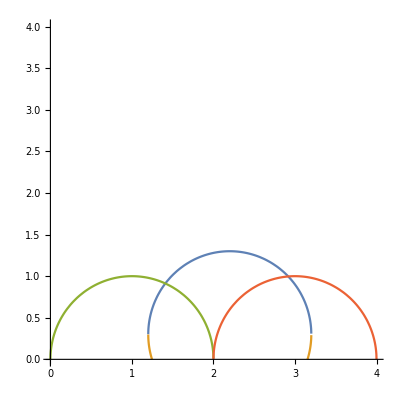

{}

{}

{{x→2.91747}}

{{x→1.40941}}

{{x→1.04971},{x→2.15029}}

{}

```mathematica
r=1;
X=2.2;Y=.3;
XL=1;YL=0;
XR=3;YR=0;
Plot[
{√(r^2-(x-X)^2)+Y,-√(r^2-(x-X)^2)+Y,
√(r^2-(x-XL)^2)+YL,
√(r^2-(x-XR)^2)+YR},{x,0,4},AspectRatio->Automatic,PlotRange->{0,4}]
Solve[√(r^2-(x-XR)^2)+YR==-√(r^2-(x-X)^2)+Y,x]
Solve[√(r^2-(x-XL)^2)+YL==-√(r^2-(x-X)^2)+Y,x]
Solve[√(r^2-(x-XR)^2)+YR==√(r^2-(x-X)^2)+Y,x]
Solve[√(r^2-(x-XL)^2)+YL==√(r^2-(x-X)^2)+Y,x]
```

```mathematica
Clear["Global`*"]
(*r=1;
X=2.2;Y=.3;
XL=1;YL=0;
XR=3;YR=0;
*)

Solve[√(r^2-(x-XR)^2)+YR==-√(r^2-(x-X)^2)+Y,x]
Solve[√(r^2-(x-XL)^2)+YL==-√(r^2-(x-X)^2)+Y,x]
Solve[√(r^2-(x-XR)^2)+YR==√(r^2-(x-X)^2)+Y,x]
Solve[√(r^2-(x-XL)^2)+YL==√(r^2-(x-X)^2)+Y,x]
```

{{x→1/(2 (4 X^2-8 X XR+4 XR^2+4 Y^2-8 Y YR+4 YR^2))(4 X^3-4 X^2 XR-4 X XR^2+4 XR^3+4 X Y^2+4 XR Y^2-8 X Y YR-8 XR Y YR+4 X YR^2+4 XR YR^2-√((-4 X^3+4 X^2 XR+4 X XR^2-4 XR^3-4 X Y^2-4 XR Y^2+8 X Y YR+8 XR Y YR-4 X YR^2-4 XR YR^2)^2-4 (4 X^2-8 X XR+4 XR^2+4 Y^2-8 Y YR+4 YR^2) (X^4-2 X^2 XR^2+XR^4-4 r^2 Y^2+2 X^2 Y^2+2 XR^2 Y^2+Y^4+8 r^2 Y YR-4 X^2 Y YR-4 XR^2 Y YR-4 Y^3 YR-4 r^2 YR^2+2 X^2 YR^2+2 XR^2 YR^2+6 Y^2 YR^2-4 Y YR^3+YR^4)))},{x→1/(2 (4 X^2-8 X XR+4 XR^2+4 Y^2-8 Y YR+4 YR^2))(4 X^3-4 X^2 XR-4 X XR^2+4 XR^3+4 X Y^2+4 XR Y^2-8 X Y YR-8 XR Y YR+4 X YR^2+4 XR YR^2+√((-4 X^3+4 X^2 XR+4 X XR^2-4 XR^3-4 X Y^2-4 XR Y^2+8 X Y YR+8 XR Y YR-4 X YR^2-4 XR YR^2)^2-4 (4 X^2-8 X XR+4 XR^2+4 Y^2-8 Y YR+4 YR^2) (X^4-2 X^2 XR^2+XR^4-4 r^2 Y^2+2 X^2 Y^2+2 XR^2 Y^2+Y^4+8 r^2 Y YR-4 X^2 Y YR-4 XR^2 Y YR-4 Y^3 YR-4 r^2 YR^2+2 X^2 YR^2+2 XR^2 YR^2+6 Y^2 YR^2-4 Y YR^3+YR^4)))}}

{{x→1/(2 (4 X^2-8 X XL+4 XL^2+4 Y^2-8 Y YL+4 YL^2))(4 X^3-4 X^2 XL-4 X XL^2+4 XL^3+4 X Y^2+4 XL Y^2-8 X Y YL-8 XL Y YL+4 X YL^2+4 XL YL^2-√((-4 X^3+4 X^2 XL+4 X XL^2-4 XL^3-4 X Y^2-4 XL Y^2+8 X Y YL+8 XL Y YL-4 X YL^2-4 XL YL^2)^2-4 (4 X^2-8 X XL+4 XL^2+4 Y^2-8 Y YL+4 YL^2) (X^4-2 X^2 XL^2+XL^4-4 r^2 Y^2+2 X^2 Y^2+2 XL^2 Y^2+Y^4+8 r^2 Y YL-4 X^2 Y YL-4 XL^2 Y YL-4 Y^3 YL-4 r^2 YL^2+2 X^2 YL^2+2 XL^2 YL^2+6 Y^2 YL^2-4 Y YL^3+YL^4)))},{x→1/(2 (4 X^2-8 X XL+4 XL^2+4 Y^2-8 Y YL+4 YL^2))(4 X^3-4 X^2 XL-4 X XL^2+4 XL^3+4 X Y^2+4 XL Y^2-8 X Y YL-8 XL Y YL+4 X YL^2+4 XL YL^2+√((-4 X^3+4 X^2 XL+4 X XL^2-4 XL^3-4 X Y^2-4 XL Y^2+8 X Y YL+8 XL Y YL-4 X YL^2-4 XL YL^2)^2-4 (4 X^2-8 X XL+4 XL^2+4 Y^2-8 Y YL+4 YL^2) (X^4-2 X^2 XL^2+XL^4-4 r^2 Y^2+2 X^2 Y^2+2 XL^2 Y^2+Y^4+8 r^2 Y YL-4 X^2 Y YL-4 XL^2 Y YL-4 Y^3 YL-4 r^2 YL^2+2 X^2 YL^2+2 XL^2 YL^2+6 Y^2 YL^2-4 Y YL^3+YL^4)))}}

{{x→1/(2 (4 X^2-8 X XR+4 XR^2+4 Y^2-8 Y YR+4 YR^2))(4 X^3-4 X^2 XR-4 X XR^2+4 XR^3+4 X Y^2+4 XR Y^2-8 X Y YR-8 XR Y YR+4 X YR^2+4 XR YR^2-√((-4 X^3+4 X^2 XR+4 X XR^2-4 XR^3-4 X Y^2-4 XR Y^2+8 X Y YR+8 XR Y YR-4 X YR^2-4 XR YR^2)^2-4 (4 X^2-8 X XR+4 XR^2+4 Y^2-8 Y YR+4 YR^2) (X^4-2 X^2 XR^2+XR^4-4 r^2 Y^2+2 X^2 Y^2+2 XR^2 Y^2+Y^4+8 r^2 Y YR-4 X^2 Y YR-4 XR^2 Y YR-4 Y^3 YR-4 r^2 YR^2+2 X^2 YR^2+2 XR^2 YR^2+6 Y^2 YR^2-4 Y YR^3+YR^4)))},{x→1/(2 (4 X^2-8 X XR+4 XR^2+4 Y^2-8 Y YR+4 YR^2))(4 X^3-4 X^2 XR-4 X XR^2+4 XR^3+4 X Y^2+4 XR Y^2-8 X Y YR-8 XR Y YR+4 X YR^2+4 XR YR^2+√((-4 X^3+4 X^2 XR+4 X XR^2-4 XR^3-4 X Y^2-4 XR Y^2+8 X Y YR+8 XR Y YR-4 X YR^2-4 XR YR^2)^2-4 (4 X^2-8 X XR+4 XR^2+4 Y^2-8 Y YR+4 YR^2) (X^4-2 X^2 XR^2+XR^4-4 r^2 Y^2+2 X^2 Y^2+2 XR^2 Y^2+Y^4+8 r^2 Y YR-4 X^2 Y YR-4 XR^2 Y YR-4 Y^3 YR-4 r^2 YR^2+2 X^2 YR^2+2 XR^2 YR^2+6 Y^2 YR^2-4 Y YR^3+YR^4)))}}

{{x→1/(2 (4 X^2-8 X XL+4 XL^2+4 Y^2-8 Y YL+4 YL^2))(4 X^3-4 X^2 XL-4 X XL^2+4 XL^3+4 X Y^2+4 XL Y^2-8 X Y YL-8 XL Y YL+4 X YL^2+4 XL YL^2-√((-4 X^3+4 X^2 XL+4 X XL^2-4 XL^3-4 X Y^2-4 XL Y^2+8 X Y YL+8 XL Y YL-4 X YL^2-4 XL YL^2)^2-4 (4 X^2-8 X XL+4 XL^2+4 Y^2-8 Y YL+4 YL^2) (X^4-2 X^2 XL^2+XL^4-4 r^2 Y^2+2 X^2 Y^2+2 XL^2 Y^2+Y^4+8 r^2 Y YL-4 X^2 Y YL-4 XL^2 Y YL-4 Y^3 YL-4 r^2 YL^2+2 X^2 YL^2+2 XL^2 YL^2+6 Y^2 YL^2-4 Y YL^3+YL^4)))},{x→1/(2 (4 X^2-8 X XL+4 XL^2+4 Y^2-8 Y YL+4 YL^2))(4 X^3-4 X^2 XL-4 X XL^2+4 XL^3+4 X Y^2+4 XL Y^2-8 X Y YL-8 XL Y YL+4 X YL^2+4 XL YL^2+√((-4 X^3+4 X^2 XL+4 X XL^2-4 XL^3-4 X Y^2-4 XL Y^2+8 X Y YL+8 XL Y YL-4 X YL^2-4 XL YL^2)^2-4 (4 X^2-8 X XL+4 XL^2+4 Y^2-8 Y YL+4 YL^2) (X^4-2 X^2 XL^2+XL^4-4 r^2 Y^2+2 X^2 Y^2+2 XL^2 Y^2+Y^4+8 r^2 Y YL-4 X^2 Y YL-4 XL^2 Y YL-4 Y^3 YL-4 r^2 YL^2+2 X^2 YL^2+2 XL^2 YL^2+6 Y^2 YL^2-4 Y YL^3+YL^4)))}}

```mathematica
r=1;
X=2.2;Y=.3;
XL=1;YL=0;
XR=3;YR=0;
x->(4 X^3-4 X^2 XR-4 X XR^2+4 XR^3+4 X Y^2+4 XR Y^2-√((-4 X^3+4 X^2 XR+4 X XR^2-4 XR^3-4 X Y^2-4 XR Y^2)^2-4 (4 X^2-8 X XR+4 XR^2+4 Y^2) (X^4-2 X^2 XR^2+XR^4-4 r^2 Y^2+2 X^2 Y^2+2 XR^2 Y^2+Y^4)))/(2 (4 X^2-8 X XR+4 XR^2+4 Y^2))
x->(4 X^3-4 X^2 XR-4 X XR^2+4 XR^3+4 X Y^2+4 XR Y^2+√((-4 X^3+4 X^2 XR+4 X XR^2-4 XR^3-4 X Y^2-4 XR Y^2)^2-4 (4 X^2-8 X XR+4 XR^2+4 Y^2) (X^4-2 X^2 XR^2+XR^4-4 r^2 Y^2+2 X^2 Y^2+2 XR^2 Y^2+Y^4)))/(2 (4 X^2-8 X XR+4 XR^2+4 Y^2))

x->(4 X^3-4 X^2 XL-4 X XL^2+4 XL^3+4 X Y^2+4 XL Y^2-√((-4 X^3+4 X^2 XL+4 X XL^2-4 XL^3-4 X Y^2-4 XL Y^2)^2-4 (4 X^2-8 X XL+4 XL^2+4 Y^2) (X^4-2 X^2 XL^2+XL^4-4 r^2 Y^2+2 X^2 Y^2+2 XL^2 Y^2+Y^4)))/(2 (4 X^2-8 X XL+4 XL^2+4 Y^2))
x->(4 X^3-4 X^2 XL-4 X XL^2+4 XL^3+4 X Y^2+4 XL Y^2+√((-4 X^3+4 X^2 XL+4 X XL^2-4 XL^3-4 X Y^2-4 XL Y^2)^2-4 (4 X^2-8 X XL+4 XL^2+4 Y^2) (X^4-2 X^2 XL^2+XL^4-4 r^2 Y^2+2 X^2 Y^2+2 XL^2 Y^2+Y^4)))/(2 (4 X^2-8 X XL+4 XL^2+4 Y^2))
```

x→2.28253

x→2.91747

x→1.40941

x→1.79059

x→2.28253

x→2.91747

x→1.40941

x→1.79059